```mathematica
Clear["p","m","x","g","gg","λ","Δt","length","rnd","θ","n","Δξ","Δζ","y"]
$Assumptions=x>0&&x∈Reals&&λ>0&&λ∈Reals&&θ>0&&θ∈Reals;
θ=√π ;
λ=50;
Δt=1/10000;
step = Round[1/(λ Δt)]
𝒟=HalfNormalDistribution[θ];
p=PDF[𝒟,x]
m=Mean[𝒟]
K2=FullSimplify[-2 λ/p Integrate[(x-m)p,{x,0,x}]](*g^2[x]*)
f[x_]=-λ(x-m)
g[x_]=Sqrt[K2]
ggt[x_]=FullSimplify[g[x] D[g[x],x]]
fgt[x_]=FullSimplify[f[x]D[g[x],x]]
g2gtt[x_]=FullSimplify[g[x]^2 D[g[x],{x,2}]]
ftg[x_]=FullSimplify[D[f[x],x] g[x]]
gggt[x_]=FullSimplify[g[x] D[ggt[x],x]]
fft[x_]=FullSimplify[f[x] D[f[x],x]]
ggt2[x_]=FullSimplify[g[x] D[g[x],x]^2]
```

200

Piecewise[{{(2 ⅇ^(-x^2))/(√π), x>0}, {0, True}}]

1/(√π)

50-50 ⅇ^(x^2) Erfc[x]

-50 (-1/(√π)+x)

√(50-50 ⅇ^(x^2) Erfc[x])

50 (1/(√π)-ⅇ^(x^2) x Erfc[x])

(250 √2 (-1+√π x) (-1+ⅇ^(x^2) √π x Erfc[x]))/(π √(1-ⅇ^(x^2) Erfc[x]))

(250 √2 (-1+2 √π x+ⅇ^(x^2) π Erfc[x] (-1-2 x^2+ⅇ^(x^2) (1+x^2) Erfc[x])))/(π √(1-ⅇ^(x^2) Erfc[x]))

-250 √(2-2 ⅇ^(x^2) Erfc[x])

50 √(50-50 ⅇ^(x^2) Erfc[x]) ((2 x)/(√π)-ⅇ^(x^2) (1+2 x^2) Erfc[x])

2500 (-1/(√π)+x)

(250 √2 (-1+ⅇ^(x^2) √π x Erfc[x])^2)/(π √(1-ⅇ^(x^2) Erfc[x]))

```mathematica
length = 2000; (* Longer sequence will result in Im[y]≠0*)
SeedRandom[1]
rnd=RandomVariate[NormalDistribution[],length];
rnd2=RandomVariate[NormalDistribution[],length];
ΔW[n_Integer]:=rnd[[n]] √Δt
ΔZ[n_Integer]:=rnd2[[n]] √Δt
Δξ[n_Integer]:=rnd[[n]] √Δt
vals=RecurrenceTable[{y[n+1]==1/(1+λ Δt)(y[n]+ λ m Δt+g[y[n]]Δξ[n]+1/2 ggt[y[n]](Δξ[n]^2-Δt)),y[1]==0.1},y,{n,1,length}];
(* The implementation of Eq. (11) in  "Implicit Taylor methods for stiff stochastic differential equations" by T. Tian and K. Burrage -- Similar to Kloeden and Platen, "Higher-order implicit strong numerical schemes for stochastic differential equations", Eq. (4.11)  *)
vals2=RecurrenceTable[{y[n+1]==1/(1+λ Δt+(λ^2 Δt^2)/2)(λ m Δt(1+λ/2 Δt)+y[n]+g[y[n]]ΔW[n]+1/2 ggt[y[n]](ΔW[n]^2-Δt)
+1/2(fgt[y[n]]+1/2 g2gtt[y[n]]-ftg[y[n]])Δt(ΔW[n]-ΔZ[n]/(√3))
+1/6 gggt[y[n]](ΔW[n]^3-3Δt ΔW[n])),y[1]==.1},y,{n,1,length}];
{{FirstPosition[vals,_Complex],FirstCase[vals,_Complex]},{FirstPosition[vals2,_Complex],FirstCase[vals2,_Complex]}}
```

{{Missing[NotFound],Missing[NotFound]},{Missing[NotFound],Missing[NotFound]}}

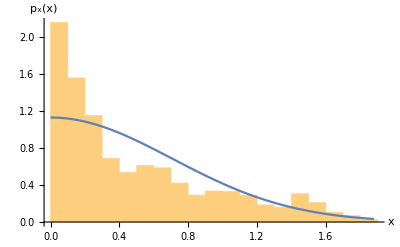

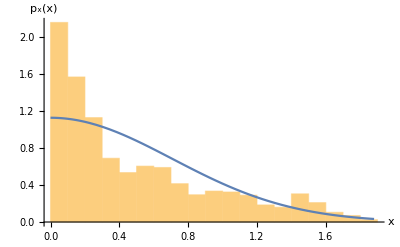

```mathematica
spoint =Solve[PDF[𝒟,x]==5 10^-3][[All,1,2]][[1]];
h1= Histogram[vals,Automatic,"PDF",ChartLegends->Placed[SwatchLegend[{"Hist"}],Scaled[{.5,1}]],PerformanceGoal->"Speed",PlotRange->{{0,Max[vals]},{0,Automatic}},AxesLabel-> {"x","p_x(x)"}];
h2=Plot[PDF[𝒟,x],{x,0,Max[vals]},PlotLegends->Placed[LineLegend[{"PDF"}],Scaled[{.5,1}]]];
pdfPlot=Show[h1,h2,LabelStyle -> Directive[Black,13,FontFamily-> "Times New Roman"],AxesLabel-> {"x","p_x(x)"},
TicksStyle->Directive[Black, 13,FontFamily-> "Times New Roman"]]
h1b= Histogram[vals2,Automatic,"PDF",ChartLegends->Placed[SwatchLegend[{"Hist"}],Scaled[{.5,1}]],PerformanceGoal->"Speed",PlotRange->{{0,Max[vals2]},{0,Automatic}},AxesLabel-> {"x","p_x(x)"}];
h2b=Plot[PDF[𝒟,x],{x,0,Max[vals2]},PlotLegends->Placed[LineLegend[{"PDF"}],Scaled[{.5,1}]]];
pdfPlotb=Show[h1b,h2b,LabelStyle -> Directive[Black,13,FontFamily-> "Times New Roman"],AxesLabel-> {"x","p_x(x)"},
TicksStyle->Directive[Black, 13,FontFamily-> "Times New Roman"]]
```

200

The null hypothesis that the data is distributed according to the HalfNormalDistribution[√π] is not rejected at the 0.1 percent level based on the Kolmogorov-Smirnov test.

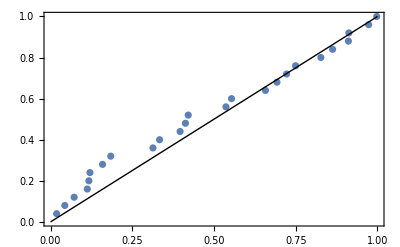

```mathematica
step = Round[1/(λ Δt)]
DistributionFitTest[vals[[1;;;;step]],𝒟,"TestConclusion",SignificanceLevel->0.001]
ProbabilityPlot[vals[[1;;;;step]],𝒟]
```